```mathematica
NetInitialize[NetChain[{LinearLayer[1]},"Input"->1]]
```

NetChain[<>]

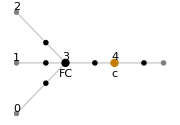

{NetChain[<>],-1.52473,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{
net=NetInitialize[NetChain[{LinearLayer[1]},"Input"->1]],
net[1]//First,
NetInformation[net,"MXNetNodeGraphPlot"],
NetInformation[net,"SummaryGraphic"],
NetInformation[net,"LayersGraph"]
}
```

```mathematica
ClassifierMeasurementsObject[net]
```

ClassifierMeasurementsObject[NetChain[<>]]

```mathematica
tune[#, 1]&/@Range[0,1,0.01]//ListAnimate
```

```mathematica
NetTrain[datum]
```

```mathematica
NetExtract[net,{All,"Weights"}]
```

{{{-1.52473}}}

```mathematica
params=NetExtract[net,{{All,"Weights"},{All,"Biases"}}]//Flatten
```

{1.16308,-3.83078}

```mathematica
haha
```

```mathematica
net[1]
```

{-1.52473}

```mathematica
format[{x_,y_}]:={x}->{y};
```

```mathematica
model=NetTrain[net,format/@datum];
params=NetExtract[model,{{All,"Weights"},{All,"Biases"}}]//Flatten;
```

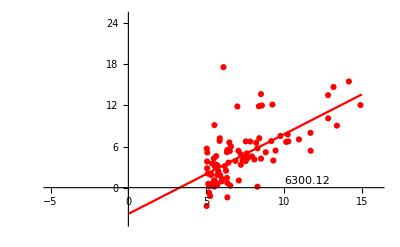

```mathematica
tune@@params
```

```mathematica
haha
```

```mathematica
tune@@params
```

-Graphics-

how about a simple predictor that overfits!

## let the neural network calculate its own line